```mathematica
file1=file4;
```

```mathematica
Dimensions@file4
```

{12063,7}

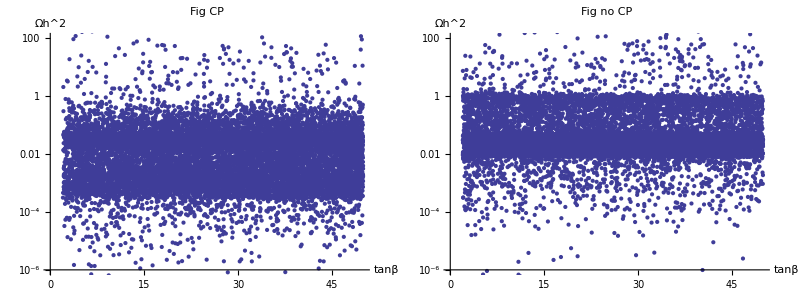

```mathematica
p1=ListLogPlot[Transpose@{file1[[;;,2,8]],file1[[;;,6,1]]},PlotLabel->label1,AxesLabel->{"tanβ","Ωh^2"},ImageSize->400,PlotRange->{Automatic,{10^-6,100}}];
p2=ListLogPlot[Transpose@{file4[[;;,2,8]],file4[[;;,6,1]]},PlotLabel->label2,AxesLabel->{"tanβ","Ωh^2"},ImageSize->400,PlotRange->{Automatic,{10^-6,100}}];
TableForm@{{p1,p2}}
```

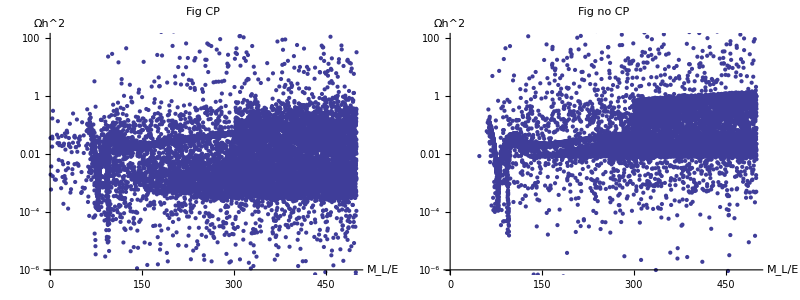

```mathematica
p1=ListLogPlot[Transpose@{file1[[;;,2,4]],file1[[;;,6,1]]},PlotLabel->label1,AxesLabel->{"M_L/E","Ωh^2"},ImageSize->400,PlotRange->{Automatic,{10^-6,100}}];
p2=ListLogPlot[Transpose@{file4[[;;,2,4]],file4[[;;,6,1]]},PlotLabel->label2,AxesLabel->{"M_L/E","Ωh^2"},ImageSize->400,PlotRange->{Automatic,{10^-6,100}}];
TableForm@{{p1,p2}}
```

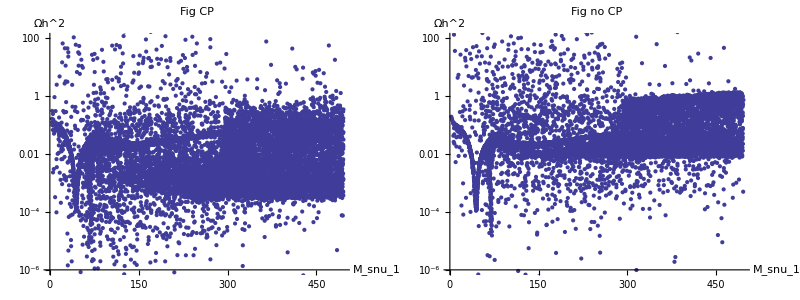

```mathematica
p1=ListLogPlot[Transpose@{file1[[;;,3,5,1]],file1[[;;,6,1]]},PlotLabel->label1,AxesLabel->{"M_snu_1","Ωh^2"},ImageSize->400,PlotRange->{Automatic,{10^-6,100}}];
p2=ListLogPlot[Transpose@{file4[[;;,3,5,1]],file4[[;;,6,1]]},PlotLabel->label2,AxesLabel->{"M_snu_1","Ωh^2"},ImageSize->400,PlotRange->{Automatic,{10^-6,100}}];
TableForm@{{p1,p2}}
```

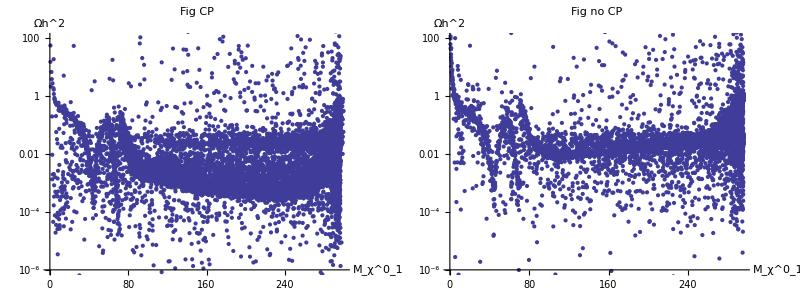

```mathematica
p1=ListLogPlot[Transpose@{Abs@file1[[;;,3,1,1]],file1[[;;,6,1]]},PlotLabel->label1,AxesLabel->{"M_χ^0_1","Ωh^2"},ImageSize->400,PlotRange->{Automatic,{10^-6,100}}];
p2=ListLogPlot[Transpose@{Abs@file4[[;;,3,1,1]],file4[[;;,6,1]]},PlotLabel->label2,AxesLabel->{"M_χ^0_1","Ωh^2"},ImageSize->400,PlotRange->{Automatic,{10^-6,100}}];
TableForm@{{p1,p2}}
```

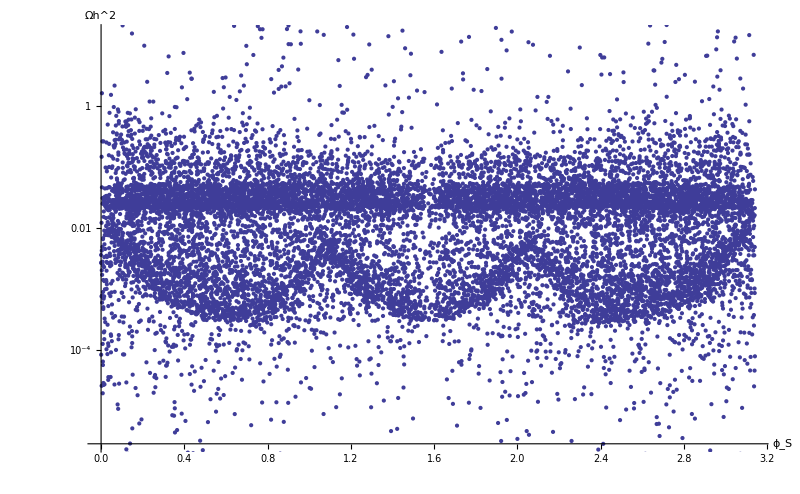

```mathematica
ListLogPlot[Transpose@{Mod[file1[[;;,2,24]],Pi],file1[[;;,6,1]]},AxesLabel->{"ϕ_S","Ωh^2"},ImageSize->800]
(* Sine behavior of Ω as a fucntion of ϕS *)
```

```mathematica
p1=ListPointPlot3D[Transpose@{Abs@file1[[;;,3,1,1]],file1[[;;,2,4]],Log[10,file1[[;;,6,1]]]},PlotLabel->label1,AxesLabel->{"M_χ^0_1","M_L/E","Ωh^2"},BoxRatios->{1,1,1},PlotRange->{{0,300},{0,500},{-6,2}},ImageSize->400];
p2=ListPointPlot3D[Transpose@{Abs@file4[[;;,3,1,1]],file4[[;;,2,4]],Log[10,file4[[;;,6,1]]]},PlotLabel->label2,AxesLabel->{"M_χ^0_1","M_L/E","Ωh^2"},BoxRatios->{1,1,1},PlotRange->{{0,300},{0,500},{-6,2}},ImageSize->400];
```

```mathematica
TableForm@{{p1,p2}}
```

-Graphics3D- | -Graphics3D-

```mathematica
Show[p1,p2]
```

-Graphics3D-